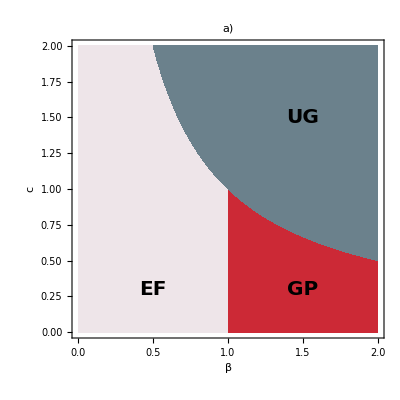

```mathematica
(*Phase Regions with Colors*)PhasePlot=Show[(*Graphics[{Thick,Blue,Line[{{1,0},{1,1}}]}],*)
RegionPlot[x<1&&x y<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->None],(*Solid Phase*)RegionPlot[x>1&&x y<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->None],(*Liquid Phase*)RegionPlot[x y>1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->None],(*Gas Phase*)(*Boundary Lines*)
Graphics[{Text[Style["EF",20,Bold,Black],{0.5,0.3}],(*Solid Region*)Text[Style["GP",20,Bold,Black],{1.5,0.3}],(*Liquid Region*)
Text[Style["UG",20,Bold,Black],{1.5,1.5}]  (*Gas Region*)}],Axes->True,AxesLabel->{"β","c"}
];

(*Show the phase diagram*)


(*Define the boundary lines*)
(*BoundaryLines={Dashed,Black,Line[{{0,1},{1,1}}]};*)

(*Show the phase diagram with boundaries*)
Show[PhasePlot,Axes->True,AxesLabel->{"β","c"},PlotLabel->"a)",PlotRange->{{0,2},{0,2}}]
```

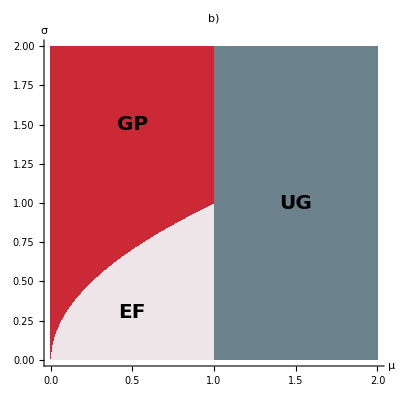

```mathematica
PhasePlot=Show[(*Gas Phase*)(*Boundary Lines*)
Graphics[{{Thick,Dashed,Black,Table[Line[{{x,x^2}}],{x,0,1,0.03}]}},Axes->False],

RegionPlot[x<1&&y^2/x<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->None],(*Solid Phase*)RegionPlot[y^2/x>1&&x <1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->None],(*Liquid Phase*)RegionPlot[x >1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->None],
Graphics[{Text[Style["EF",20,Bold,Black],{0.5,0.3}],(*Solid Region*)Text[Style["GP",20,Bold,Black],{0.5,1.5}],(*Liquid Region*)
Text[Style["UG",20,Bold,Black],{1.5,1}]  (*Gas Region*)}]
];

(*Show the phase diagram with boundaries*)
Show[PhasePlot,(*Graphics[{{Thick,Dashed,Black,Table[Line[{{x,x^2}}],{x,0,1,0.03}]}}],*)Axes->True,AxesLabel->{Style["μ",23,Black],Style["σ",23,Black]},LabelStyle->{Bold,14},PlotRange->Full,PlotLabel->"b)"]
```

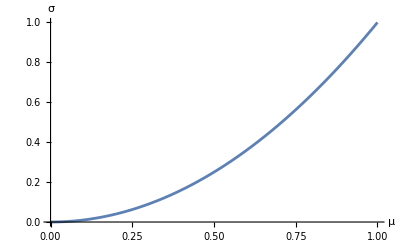

```mathematica
Show[Plot[x^2,{x,0,1}],AxesLabel->{"μ","σ"}]
```

1

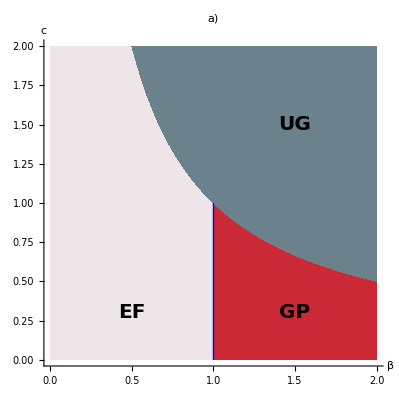

```mathematica
ga=1
PhasePlot2=Show[Graphics[{Thick,Blue,Line[{{1,0},{1,1}}]}],RegionPlot[x<1&&x y<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->None],(*Solid Phase*)RegionPlot[x>1&&x y<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->None],(*Liquid Phase*)RegionPlot[x y>1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->None],(*Gas Phase*)(*Boundary Lines*)
Graphics[{Text[Style["EF",20,Bold,Black],{0.5,0.3}],(*Solid Region*)Text[Style["GP",20,Bold,Black],{1.5,0.3}],(*Liquid Region*)
Text[Style["UG",20,Bold,Black],{1.5,1.5}]}] ,
AxesLabel->{Style["β",20],Style["c",20]},LabelStyle->{Bold,14}
];

(*Show the phase diagram*)


(*Define the boundary lines*)
BoundaryLines={Dashed,Black,Line[{{0,1},{2,1}}]};

(*Show the phase diagram with boundaries*)
Show[PhasePlot2,(*Graphics[BoundaryLines],*)Axes->True,AxesLabel->{Style["β",23,Black],Style["c",23,Black]},PlotLabel->"a)"]
```

0.5

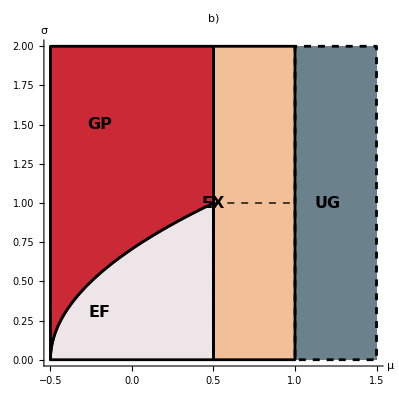

```mathematica
g=0.5
PhasePlot2=Show[(*Gas Phase*)(*Boundary Lines*)
Graphics[{{Thick,Dashed,Black,Table[Line[{{x,x^2}}],{x,0,1,0.03}]}},Axes->False],

RegionPlot[x<1-g&&y^2/(x+g)<1,{x,-g,1.5},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->Black],(*Solid Phase*)RegionPlot[y^2/(x+g)>1&&x <1-g,{x,-g,1.5},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->Black],(*Liquid Phase*)RegionPlot[x >1-g&&x<1,{x,-g,1.5},{y,0,2},PlotStyle->RGBColor["#F1BF98"],BoundaryStyle->Black],RegionPlot[x >1,{x,-1,1.5},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->{Black,Dashed}],
Graphics[{Text[Style["EF",16,Bold,Black],{-0.2,0.3}],(*Solid Region*)Text[Style["GP",16,Bold,Black],{-0.2,1.5}],(*Liquid Region*)
Text[Style["EX",16,Bold,Black],{0.5,1}]  ,Text[Style["UG",16,Bold,Black],{1.2,1}]  (*Gas Region*)}]
];

(*Show the phase diagram with boundaries*)
Show[PhasePlot2,Graphics[{{Thick,Dashed,Black,Table[Line[{{x,(x+g)^2}}],{x,-g,1,0.03}]},{Thick,Dashed,Black,Line[{{g,1},{1,1}}]}},Axes->False],Axes->True,AxesLabel->{"μ","σ"},PlotRange->Full,PlotLabel->"b)"]
```

```mathematica
PhasePlot=Show[(*Gas Phase*)(*Boundary Lines*)
Graphics[{{Thick,Dashed,Black,Table[Line[{{x,x^2}}],{x,0,1,0.03}]}},Axes->False],

RegionPlot[x<1&&y^2/x<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->None],(*Solid Phase*)RegionPlot[y^2/x>1&&x <1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->None],(*Liquid Phase*)RegionPlot[x >1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->None],
Graphics[{Text[Style["EF",20,Bold,Black],{0.5,0.3}],(*Solid Region*)Text[Style["GP",20,Bold,Black],{0.5,1.5}],(*Liquid Region*)
Text[Style["UG",20,Bold,Black],{1.5,1}]  (*Gas Region*)}]
];

(*Show the phase diagram with boundaries*)
Show[PhasePlot,(*Graphics[{{Thick,Dashed,Black,Table[Line[{{x,x^2}}],{x,0,1,0.03}]}}],*)Axes->True,AxesLabel->{"μ","σ"},LabelStyle->{Bold,14},PlotRange->Full,PlotLabel->"b)"]
```